```mathematica
LargeDensity=(8750000-6500000)/22500;
OverallDurationSum=Import[NotebookDirectory[]<>"overall_duration_sum.csv","CSV"];
h2[k_,p_,h1_]:=Max[0,(-Log[1/k]+h1 Log[p])/Log[p]];
```

#### Productivity

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

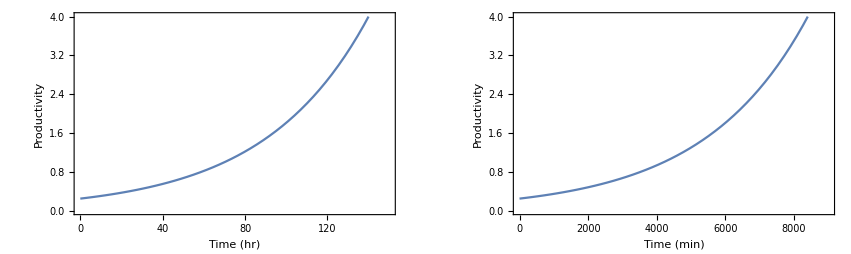

```mathematica
Productivity[h_]:=0.25*1.02^h;
GraphicsArray[{
Plot[Productivity[h],{h,0,150}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (hr)", "Productivity"}],
Plot[Productivity[m/60],{m,0,9000}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (min)", "Productivity"}]}]
```

GraphicsArray::obs: GraphicsArray is obsolete. Switching to GraphicsGrid.

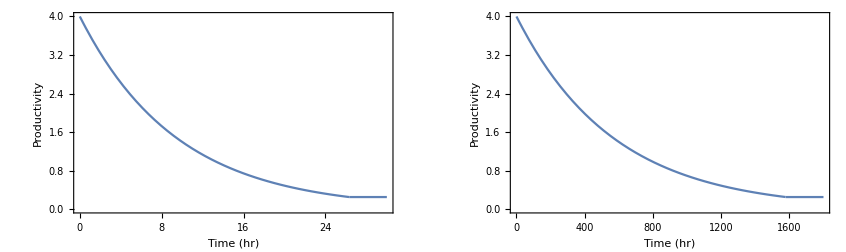

```mathematica
GraphicsArray[{
Plot[Max[4*0.9^h,0.25],{h,0,30}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (hr)", "Productivity"}],
Plot[Max[4*0.9^(m/60),0.25],{m,0,1800}, Frame->True, PlotRange->{0,4},FrameLabel->{"Time (hr)", "Productivity"}]}]
```

#### Maximal toy duration can be used within that size

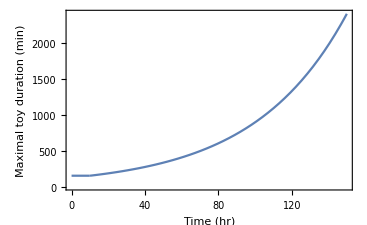

```mathematica
MaximalToyDuration[m_]:=Max[150,600*0.25*1.02^(m-10)];
Plot[MaximalToyDuration[m],{m,0,150}, Frame->True, PlotRange->{0,2400},FrameLabel->{"Time (hr)", "Maximal toy duration (min)"}]
```

#### Compensation toy distribution

Since the largest toys (duration ~ 22500) will always end up with a productivity rate 0.25, we can use the small toys to raise that rate, and then produce large toys w/ productivity rate >0.25, hence save time. 
Therefore, the problem turns to be, how to distribute the small toys, so we can save more time on the large toys (comparing to produce all of them in the productivity rate 0.25).
Use calculus of variations, in case assuming that the available “small” toy duration sum is a constant.

```mathematica
Δh[k_,p_,h_,h1_]:=(1/(1/4)-1/(1/4*p^h1))+k(1/(1/4)-1/(1/4*p^(h-h1)));
```

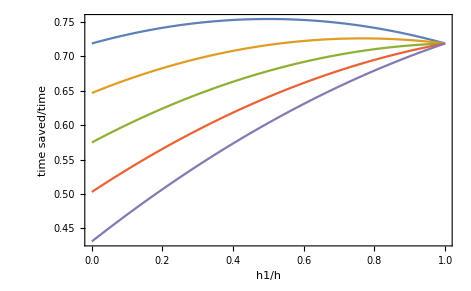

```mathematica
Plot[{
Δh[1,1.02,h,h*h1overh]/.h->10,
Δh[0.9,1.02,h,h*h1overh]/.h->10,
Δh[0.8,1.02,h,h*h1overh]/.h->10,
Δh[0.7,1.02,h,h*h1overh]/.h->10,
Δh[0.6,1.02,h,h*h1overh]/.h->10,
},{h1overh,0,1},Frame->True, FrameLabel->{"h1/h", "time saved/time"}]
```

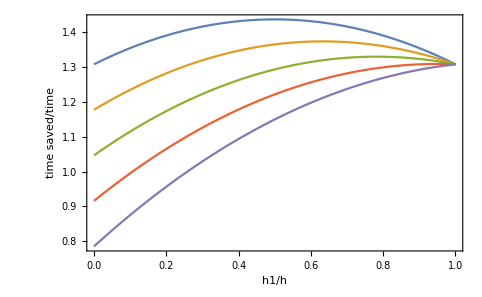

```mathematica
Plot[{
Δh[1,1.02,h,h*h1overh]/.h->20,
Δh[0.9,1.02,h,h*h1overh]/.h->20,
Δh[0.8,1.02,h,h*h1overh]/.h->20,
Δh[0.7,1.02,h,h*h1overh]/.h->20,
Δh[0.6,1.02,h,h*h1overh]/.h->20,
},{h1overh,0,1},Frame->True, FrameLabel->{"h1/h", "time saved/time"}]
```

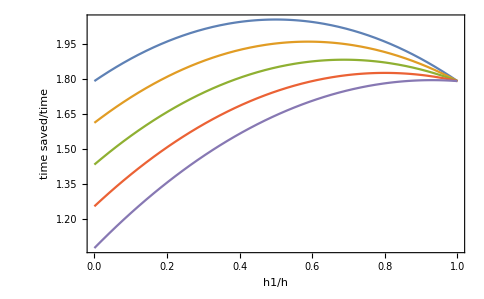

```mathematica
Plot[{
Δh[1,1.02,h,h*h1overh]/.h->30,
Δh[0.9,1.02,h,h*h1overh]/.h->30,
Δh[0.8,1.02,h,h*h1overh]/.h->30,
Δh[0.7,1.02,h,h*h1overh]/.h->30,
Δh[0.6,1.02,h,h*h1overh]/.h->30,
},{h1overh,0,1},Frame->True, FrameLabel->{"h1/h", "time saved/time"}]
```

```mathematica
D[Δh[k,p,h,h1], h1]
```

4 p^-h1 Log[p]-4 k p^(-h+h1) Log[p]

```mathematica
Solve[4 p^-h1 Log[p]-4 k p^(-h+h1) Log[p]==0, h1]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{h1→(Log[1/k]+h Log[p])/(2 Log[p])}}

```mathematica
Solve[(Log[1/k]+(h1+h2)Log[p])/(2 Log[p])==h1,h2]
```

{{h2→(-Log[1/k]+h1 Log[p])/Log[p]}}

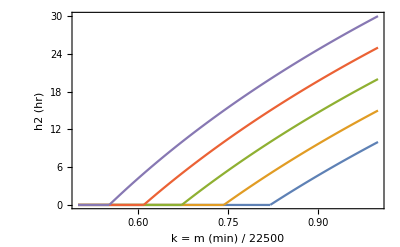

```mathematica
h2[k_,p_,h1_]:=Max[0,(-Log[1/k]+h1 Log[p])/Log[p]];
Plot[{
h2[k,1.02,10],
h2[k,1.02,15],
h2[k,1.02,20],
h2[k,1.02,25],
h2[k,1.02,30],
},{k,0.5,1},Frame->True,PlotRange->{0,30},FrameLabel->{"k = m (min) / 22500","h2 (hr)"}]
```

```mathematica
22500*LargeDensity*60∫_0^1 h2[k,1.02,10]ⅆk
22500*LargeDensity*60∫_0^1 h2[k,1.02,15]ⅆk
22500*LargeDensity*60∫_0^1 h2[k,1.02,20]ⅆk
22500*LargeDensity*60∫_0^1 h2[k,1.02,25]ⅆk
22500*LargeDensity*60∫_0^1 h2[k,1.02,30]ⅆk
```

1.25265×10^8

2.7306×10^8

4.70555×10^8

7.13064×10^8

9.96343×10^8

#### Possible compensation toy available

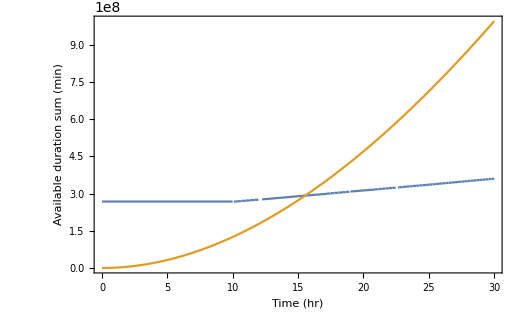

```mathematica
Plot[{
OverallDurationSum[[Floor[MaximalToyDuration[m]-1]]][[2]],
22500*LargeDensity*60∫_0^1 h2[k,1.02,m]ⅆk,
},{m,0,30}, Frame->True,FrameLabel->{"Time (hr)", "Available duration sum (min)"}]
```

#### Compensation time for largest toy

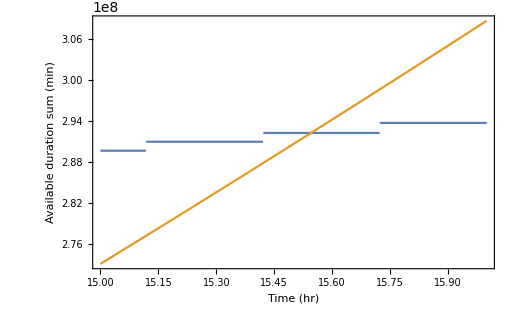

```mathematica
Plot[{
OverallDurationSum[[Floor[MaximalToyDuration[m]-1]]][[2]],
22500*LargeDensity*60∫_0^1 h2[k,1.02,m]ⅆk,
},{m,15,16}, Frame->True,FrameLabel->{"Time (hr)", "Available duration sum (min)"}]
```

Therefore, m = 15.52

#### Theoretical packing time before compensation

Naive way, ~ First Available Elf Benchmark 1875730155.0575

```mathematica
(24/10*LargeDensity*∫_0^22500 4*mⅆm)/900*Log[1+900]//N
```

1.83695×10^9

#### Theoretical packing time after compensation

```mathematica
(24/10*LargeDensity*∫_0^22500 4/1.02^h2[m/22500,1.02,15.52]*mⅆm)/900*Log[1+900]//N
```

1.70834×10^9

```mathematica
(24/10*LargeDensity*∫_2400^22500 4/1.02^h2[h/22500,1.02,15.52]*mⅆm)/900*Log[1+900]//N
```

1.68744×10^9

#### Theoretical packing time if the largest possible number of toys start from productivity 0.25

Use all <=2400 toys, rectangle distribution:

```mathematica
handleNum=OverallDurationSum[[2400]][[2]]/8400/100//N
(24/10*LargeDensity*(∫_0^(22500-handleNum) 4*hⅆh+∫_(22500-handleNum)^22500 0.25*hⅆh))/900*Log[1+900]//N
```

1265.4

1.64869×10^9

Use all <=2400 toys, triangle distribution:

```mathematica
Solve[{k*22500+b==8400,k*(22500-handleNum*2)+b==0},{k,b}]
```

{{k→3.31911,b→-66280.1}}

```mathematica
(24/10*LargeDensity*∫_0^22500 4/1.02^Max[0, 3.31911 h-66280]*hⅆh)/900*Log[1+900]//N
```

1.44916×10^9

Use all <=600 toys, rectangle distribution:

```mathematica
handleNum=OverallDurationSum[[600]][[2]]/4200/100//N
(24/10*LargeDensity*(∫_0^(22500-handleNum) 4*hⅆh+∫_(22500-handleNum)^22500 1*hⅆh))/900*Log[1+900]//N
```

1438.1

1.66646×10^9

It is even better than the complicated compensation model.
So the compensation model is not correct, because we shouldn’t assume that the overall compensation duration sum is a constant. The reason is that  a condition w/ higher productivity rate (hence longer compensation time) can use toys w/ longer duration, while the ones w/ lower productivity rate can’t

#### If by successful packing, all <2400min duration toys can be used for compensation, but the original curve is still in some sense reasonable

```mathematica
FindRoot[22500*LargeDensity*60∫_0^1 h2[k,1.02,m]ⅆk==1062934090,{m,30}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{m→31.0869}

```mathematica
(24/10*LargeDensity*∫_0^22500 4/1.02^h2[m/22500,1.02,31.0869]*mⅆm)/900*Log[1+900]//N
```

1.44878×10^9

It is only a little bit better then the triangle setup ~1.44915×10^9

#### Aggresive lower limit

Since the toys w/ duration <=mmin can *lower* the productivity rate to 0.25, while the toys w/ duration <=mmax can *keep* the productivity rate in 0.25.

```mathematica
mmax=Ceiling[2400*((h/.Solve[1.02^10*0.9^h==1,h][[1]])+10)/10]
mmin=Ceiling[2400*(4/1.02^10)/4]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

2852

1969

```mathematica
OverallDurationSum[[mmin]][[2]];
FindRoot[22500*LargeDensity*60∫_0^1 h2[k,1.02,m]ⅆk==%,{m,30}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{m→29.2331}

```mathematica
(24/10*LargeDensity*∫_mmax^22500 4/1.02^h2[m/22500,1.02,29.2331]*mⅆm)/900*Log[1+900]//N
```

1.45264×10^9

#### Absolute absolute lower limit

Assume toys w/ duration in between [mmin, mmax] can still raise the duration rate in the original way, which is not true.

```mathematica
OverallDurationSum[[mmax]][[2]];
FindRoot[22500*LargeDensity*60∫_0^1 h2[k,1.02,m]ⅆk==%,{m,30}]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{m→33.0624}

```mathematica
(24/10*LargeDensity*∫_mmax^22500 4/1.02^h2[m/22500,1.02,33.0624]*mⅆm)/900*Log[1+900]//N
```

1.38347×10^9

#### Mistake for above calculation

The time count for calculate the productivity rate, is the real time(after scaling), rather than the theoretical time needed. Will analyse in another document.